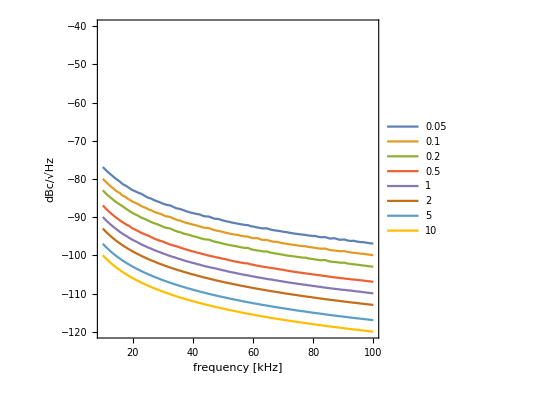

```mathematica
lifetime= 1/(π^2(f*1000)^2 10^(SfdBc/10));
τvals = {0.05,0.1,0.2,0.5,1,2,5,10};
ContourPlot[Evaluate[Table[lifetime==τ,{τ,τvals}]],{f,10,100},{SfdBc,-40,-120},FrameLabel->{"frequency [kHz]","dBc/√Hz"},Contours->20,ContourLabels->Automatic,PlotLegends->τvals]
```

```mathematica
Sf = (3*10^-6)^2;(*(√(Hz^-1))^2*)
1/(π^2(f*1000)^2*Sf)/.f-> 10//N
```

112.579

```mathematica
20 Log[10,3*10^-6]//N
```

-110.458

Even distribution of noise, with RMS fluctuation of 6*10^-4 distributed over a 40 kHz band. this is equivalent to a single frequency spike of 3*10^-6/√Hzat 10 kHz, we

```mathematica
((√(6*10^-4))^2)/(√40000)//N
```

3.×10^-6

Can assumed fixed bandwidth and a flat noise floor, but I didn't process the data in to get the RMS fluctuations.

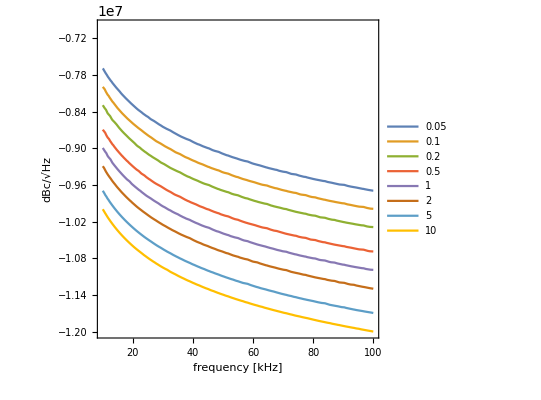

```mathematica
BW = 100000;(*the range over which we measure white noise*)
lifetime= 1/(π^2(f*1000)^2 10^((-/BW)/10));
τvals = {0.05,0.1,0.2,0.5,1,2,5,10};
ContourPlot[Evaluate[Table[lifetime==τ,{τ,τvals}]],{f,10,100},{RMSwhitenoise,-70,-120},FrameLabel->{"frequency [kHz]","dBc/√Hz"},Contours->20,PlotLegends->τvals]
```